# Ecological cycling - Null model

## Dynamics without ecological structuring

Here batchruns tells us how many realisations of the cycling to run

```mathematica
batchruns=100;
```

## Initialisation

In this section we provide definitions required for proper colours, number of strains, environments to be used

```mathematica
speciesproperties={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
base={RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]};
possibleenvs=Tuples[{0,1},4];
carryingcapacity=10;
inoculumsize=5;
negativegrowthrate=-2;(*If we put this to 0 then we get persistence*)
tmax=20;
tpool=.;
```

### The equations for growth in wells

```mathematica
xdot[i_,grrates_]:=(grrates⟦i⟧(1-(∑_(k=1)^4 Subscript[x, k][t])/carryingcapacity))Subscript[x, i][t];
```

Growth rates of the strains

```mathematica
expgr={1.028,0.282,1.564,1.103};
```

#### When we want to change the basic growth rates by a certain percent use the following code

```mathematica
(*deltas=Table[(Mean[expgr]-expgr⟦i⟧) 0.5,{i,Length[expgr]}];
expgr=expgr+deltas;*)
```

Now we make the figure for the growth rates.

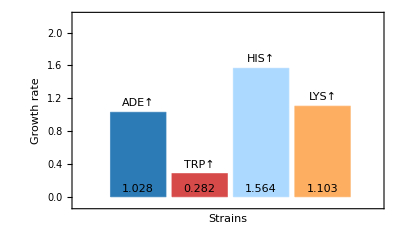

```mathematica
avggrowthrates=Flatten[Join[{0,expgr}]];
legends={"NP","ADE↑","TRP↑","HIS↑","LYS↑"};
charts=PieChart[{1,1,1,1},ChartStyle->{If[#⟦1⟧==1,base⟦1⟧,GrayLevel[0.9]], If[#⟦2⟧==1,base⟦2⟧,GrayLevel[0.9]], If[#⟦3⟧==1,base⟦3⟧,GrayLevel[0.9]], If[#⟦4⟧==1,base⟦4⟧,GrayLevel[0.9]]}]&/@speciesproperties;
BarChart[avggrowthrates⟦2;;⟧,ChartLabels->Placed[legends⟦2;;⟧,Above],ChartStyle->base,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Strains",Black,16],Style["Growth rate",Black,16]},PlotRange->{Automatic,{-0.1,2.2}},Epilog->{(*Inset[charts⟦1⟧,{1,1.4},{0,0},0.5],*)Inset[charts⟦1⟧,{1,1.4},{0,0},0.5],Inset[charts⟦2⟧,{2,1.0},{0,0},0.5],Inset[charts⟦3⟧,{3,1.65},{0,0},0.5],Inset[expgr⟦1⟧,{1,0.1}],Inset[expgr⟦2⟧,{2,0.1}],Inset[expgr⟦3⟧,{3,0.1}],Inset[expgr⟦4⟧,{4,0.1}],Inset[charts⟦4⟧,{4,1.45},{0,0},0.5]}]
```

Growth rate equations for the pool

```mathematica
poolgrrate=expgr;
ydot[i_,poolgrrate_]:=(poolgrrate⟦i⟧)Subscript[y, i][t]
```

Then we write the functions that numerically integrate the wells and the pool phases

```mathematica
rundynamics[initcond_,grrates_]:={eqs=.;sol=.;t=.;
NDSolve[Join[Table[Subscript[x, i]'[t]==xdot[i,grrates],{i,1,4}],Table[Subscript[x, i][0]==initcond⟦i⟧,{i,1,4}]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]},{t,0,tmax}]
};
pooldynamics[initcond_,tpool_]:={eqs=.;poolsol=.;t=.;
NDSolve[Join[Table[Subscript[y, i]'[t]==ydot[i,poolgrrate],{i,1,4}],Table[Subscript[y, i][0]==initcond⟦i⟧,{i,1,4}]],{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4]},{t,0,tpool}]//Quiet
};
```

#### Forming groups

```mathematica
groupsize=4;
grouped=Tuples[speciesproperties,groupsize];
```

#### Importing fitness matrix for env and community

Here we import the fitnesses as extrapolated from the experiments. For each strain the growth rate can be different if the metabolite it requires but cannot produces comes from another strain or the environment.

```mathematica
rawfit=Import[NotebookDirectory[]<>"fitnesstoimport_avg.xlsx"];
rawfit=rawfit⟦1⟧;
environments=ToExpression[rawfit⟦1,2;;⟧];
communities=ToExpression[rawfit⟦All,1⟧⟦2;;⟧];
grs=ToExpression[rawfit⟦2;;,2;;⟧];
fulldict=Association[];
fulldict={};
For[j=1,j≤Length[environments],j++,
For[i=1,i≤Length[communities],i++,
AppendTo[fulldict,{environments⟦j⟧,communities⟦i⟧}->grs⟦i,j⟧]
]
]
```

In the following we make the figure showing the fitnesses along with the colour code

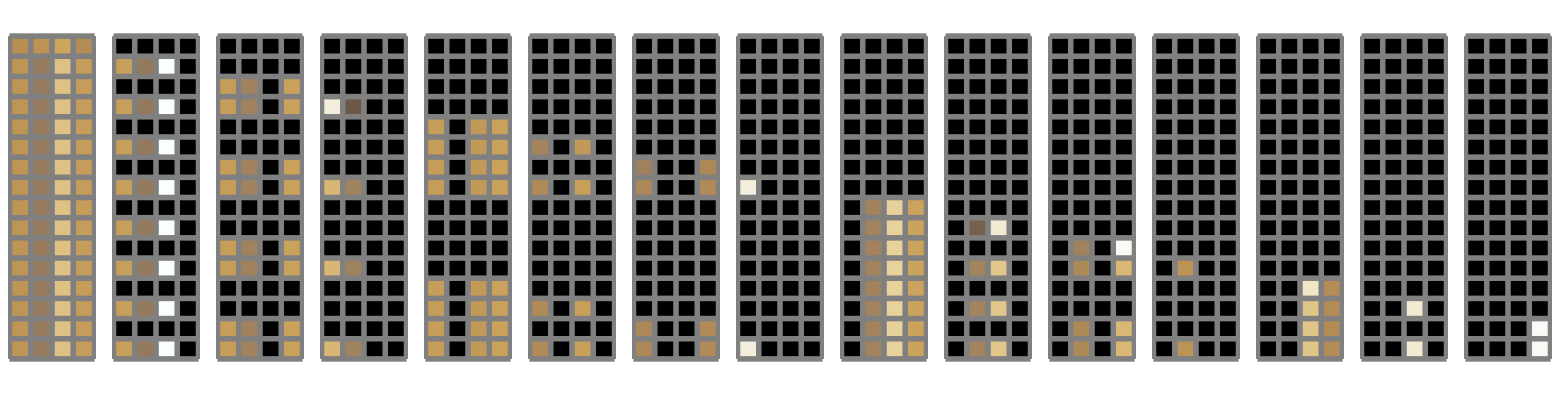

```mathematica
GraphicsRow[Table[MatrixPlot[grs⟦i⟧/.{Null->{0,0,0,0}},ColorFunction->(If[#==0,Black,ColorData["CoffeeTones"][Rescale[#,{0,2}]]]&),ColorFunctionScaling->False,Mesh->True,Frame->False,MeshStyle->Directive[{Gray,Thickness[0.01]}]],{i,Length[grs]}],Spacings->0]
BarLegend[{"CoffeeTones",{0,2}}]
```

Using the above fitnesses and the dynamics equations we show how the growth looks like in a single well.

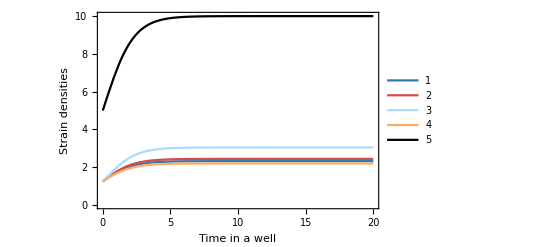

```mathematica
Plot[Evaluate[{Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[x, 4][t],Subscript[x, 1][t]+Subscript[x, 2][t]+Subscript[x, 3][t]+Subscript[x, 4][t]}/.rundynamics[{0.25,0.25,0.25,0.25} 5,Values[fulldict]⟦1⟧]],{t,0,20},PlotStyle->Flatten[Join[{base,Black}]],Frame->True,FrameStyle->{Black,Thickness[0.003]},PlotLegends->Automatic,FrameLabel->{Style["Time in a well", Black, 18],Style["Strain densities",Black, 18]}]
```

To make the process efficient we create a dictionary for the growth rates

```mathematica
allpossiblecombinations=Tuples[Tuples[{0,1},4],2];
notvalid=0;
valid={};
For[i=1,i≤Length[allpossiblecombinations],i++,If[MemberQ[Total[allpossiblecombinations⟦i⟧],0]==True||allpossiblecombinations⟦i,2⟧=={0,0,0,0},notvalid++,AppendTo[valid,i]]];
allvalidcombinations=allpossiblecombinations⟦#⟧&/@valid;
```

If choosing random fitnesses use the follow block

```mathematica
(*randomfitnesses=Table[allvalidcombinations⟦i,2⟧ RandomReal[2,4],{i,1,Length[allvalidcombinations]}];
envcommunityfitnessmatrix=Table[allvalidcombinations⟦i⟧->randomfitnesses⟦i⟧,{i,1,Length[allvalidcombinations]}];*)
```

else use this

```mathematica
envcommunityfitnessmatrix=Table[allvalidcombinations⟦i⟧->Lookup[fulldict,{allvalidcombinations⟦i⟧}]⟦1⟧,{i,1,Length[allvalidcombinations]}];
```

### Distribution of the environments

How are the environments chosen? at random or do they follow a certain distribution?

{RGBColor[0., 0., 0.],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8509803921568627, 1.],RGBColor[0.8313725490196078, 0.7666666666666666, 0.6901960784313725],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.9176470588235295, 0.4861764705882353, 0.33519607843137256],RGBColor[0.7568627450980392, 0.5704901960784313, 0.645],RGBColor[0.8352941176470587, 0.6077777777777778, 0.556797385620915],RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.5823529411764706, 0.5823529411764706, 0.5470588235294118],RGBColor[0.42156862745098034, 0.6666666666666666, 0.8568627450980393],RGBColor[0.611764705882353, 0.6718954248366013, 0.6980392156862745],RGBColor[0.5078431372549019, 0.3861764705882353, 0.5018627450980392],RGBColor[0.669281045751634, 0.4849019607843137, 0.4613725490196078],RGBColor[0.5620915032679739, 0.5411111111111111, 0.6679084967320261],RGBColor[0.6696078431372549, 0.576421568627451, 0.5960294117647059]}

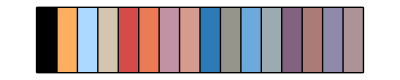

```mathematica
envcols=Blend[{RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]},#]&/@possibleenvs
ArrayPlot[{envcols},Mesh->True,MeshStyle->Black]
```

However these are not sorted by the level of richness... below we will sort the environments according to their richness level and then reorder the colours.

```mathematica
ones=Count[#,1]&/@possibleenvs;
possibleenvssorted=SortBy[Partition[Riffle[possibleenvs,ones],2],Last]⟦All,1⟧;
envcolssorted=Blend[{RGBColor[0.17254901960784313, 0.4823529411764706, 0.7137254901960784],RGBColor[0.8431372549019608, 0.29, 0.29],RGBColor[0.6705882352941176, 0.8509803921568627, 1],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451]},#]&/@possibleenvssorted;
```

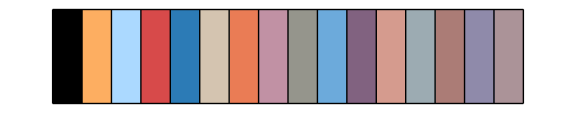

```mathematica
ArrayPlot[{envcolssorted},Mesh->True,MeshStyle->Black,ImageSize->Large]
```

Now we derive different form of environment posteriors
When the distribution is uniform then we use flat or else we draw from a Poisson distribution (in weightfun) or we can also modify the environments to select only a few to be represented as in depleted

```mathematica
flat=ConstantArray[1/16//N,16];
```

```mathematica
rans=.;
rans[λ_]:=Table[PDF[PoissonDistribution[λ],k]//Evaluate,{k,16}]//N(*RandomReal[1,16]*);
weightfun[param_]:=Module[{λ=param},randomlist=rans[λ];randomlist/Total[randomlist]];
```

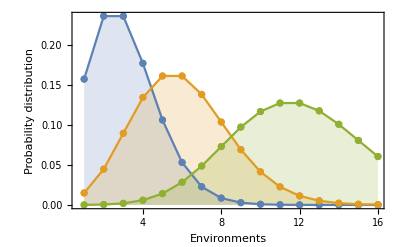

```mathematica
ListPlot[Table[weightfun[λ],{λ,{3,6,12}}],Filling->Axis,Mesh->Full,Joined->True,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],GridLines->{None,{1/16}},GridLinesStyle->Directive[Black,Thickness[0.003]],Method->{"GridLinesInFront"->True},FrameLabel->{Style["Environments",Black,18],Style["Probability distribution",Black,18]}]
```

If we want to choose the richness and then choose the environment accordingly then we pick the poor (0) to rich (4) environments as per a Poisson

```mathematica
rans=.;
poorrich[λ_]:=Table[PDF[PoissonDistribution[λ],k]//Evaluate,{k,5}]//N(*RandomReal[1,16]*);
poorrichweightfun[param_]:=Module[{λ=param},randomlist=poorrich[λ];randomlist/Total[randomlist]];
```

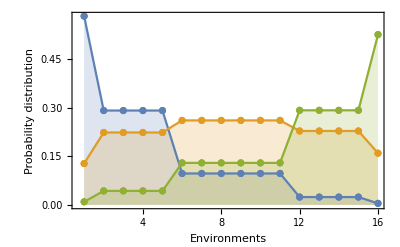

```mathematica
ListPlot[Table[{poorrichweightfun[λ]⟦1⟧,poorrichweightfun[λ]⟦2⟧,poorrichweightfun[λ]⟦2⟧,poorrichweightfun[λ]⟦2⟧,poorrichweightfun[λ]⟦2⟧,poorrichweightfun[λ]⟦3⟧,poorrichweightfun[λ]⟦3⟧,poorrichweightfun[λ]⟦3⟧,poorrichweightfun[λ]⟦3⟧,poorrichweightfun[λ]⟦3⟧,poorrichweightfun[λ]⟦3⟧,poorrichweightfun[λ]⟦4⟧,poorrichweightfun[λ]⟦4⟧,poorrichweightfun[λ]⟦4⟧,poorrichweightfun[λ]⟦4⟧,poorrichweightfun[λ]⟦5⟧},{λ,{1,3.5,9}}],Filling->Axis,Mesh->Full,Joined->True,PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],GridLines->{None,{1/16}},GridLinesStyle->Directive[Black,Thickness[0.003]],Method->{"GridLinesInFront"->True},FrameLabel->{Style["Environments",Black,18],Style["Probability distribution",Black,18]}]
```

If we want a specific metabolite to be depleted from the environment and not others.. here is an example where the TRP is depleted and all the environments having TRP are then removed.

```mathematica
trpdepleted={};
Table[If[possibleenvssorted⟦i⟧⟦2⟧==1,AppendTo[trpdepleted,0],AppendTo[trpdepleted,flat⟦i⟧]],{i,1,Length[possibleenvssorted],1}];
depleted=Normalize[trpdepleted,Total[#,∞]&];
```

Use the appropriate distribution to finally choose the weights for the environments 
Flat for Uniform
depleted for a certain metabolite removed
or weightfun which draws a Poisson Distribution with a given degree.

```mathematica
weightdistribution=Table[{poorrichweightfun[λ]⟦1⟧,(poorrichweightfun[λ]⟦2⟧)/4,(poorrichweightfun[λ]⟦2⟧)/4,(poorrichweightfun[λ]⟦2⟧)/4,(poorrichweightfun[λ]⟦2⟧)/4,(poorrichweightfun[λ]⟦3⟧)/6,(poorrichweightfun[λ]⟦3⟧)/6,(poorrichweightfun[λ]⟦3⟧)/6,(poorrichweightfun[λ]⟦3⟧)/6,(poorrichweightfun[λ]⟦3⟧)/6,(poorrichweightfun[λ]⟦3⟧)/6,(poorrichweightfun[λ]⟦4⟧)/4,(poorrichweightfun[λ]⟦4⟧)/4,(poorrichweightfun[λ]⟦4⟧)/4,(poorrichweightfun[λ]⟦4⟧)/4,poorrichweightfun[λ]⟦5⟧},{λ,{9}}]⟦1⟧(*depleted*)(*flat*)(*weightfun[12]*);
```

Visualise the distribution to be used

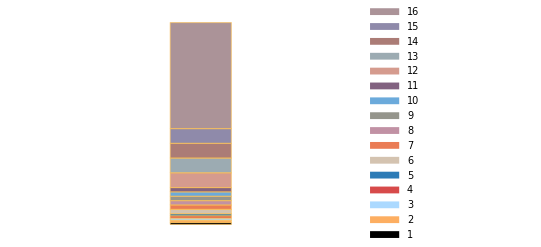

```mathematica
BarChart[weightdistribution,ChartLayout->"Stacked",ChartStyle->envcolssorted,ChartLegends->Automatic,Axes->False]
```

## Lifecycle

First define the global pool of strains
Initially in the global pool all strain are in equal frequency = 0.25 and hence all communities are equally probable. We sample on 96 for the experiment.
The time in the wells t_well=20 is already set so we can choose the time spent in the pool phase relative to it.

```mathematica
pooltimes=RecurrenceTable[{a[n+1]==2a[n],a[1]==0.02},a,{n,1,10}](*Table[2/i,{i,{100,10,1,0.1}}]//N*);
```

```mathematica
counterlist=(*pooltimes*){1.28}(*use a specific time relative to Subscript[t, well]= 20 or the above vector pooltimes*);
startfeedbackat=9;
```

startfeedbackat is the cycle number where we start the feedback of nutrients in the next pool. Currently the number is set to be larger than cycles so no feedback occurs. Try 0, 5, 9 to generate results for the parameters in the manuscript

```mathematica
meanfrequenciesofstrains={};
meandeath={};
storeenvs={};
comparingextinctions={};
For[counter=1,counter≤Length[counterlist],counter++,
tpool=counterlist⟦counter⟧;
storegraphics={};
storebarchartdata={};
extinction={};
For[batchrun=1,batchrun≤batchruns,batchrun++,
fourrans=RandomReal[1,4];
distribution=If[Length[counterlist]==1,{0.25,0.25,0.25,0.25},fourrans/Total[fourrans]//N];
totalcycles=10;
cyclegraphic={};
finalnumbers={};
finalpool={distribution};
countdeath={};
For[numberofcycle=0,numberofcycle<totalcycles,numberofcycle++,
If[distribution!={0,0,0,0},{
sampledcommunities=Table[RandomChoice[distribution->speciesproperties,4],1];
production=Total[#]&/@sampledcommunities;
prodreduced=production/.{2->1,3->1,4->1};
weights=If[numberofcycle<startfeedbackat,weightdistribution,Table[Times@@Table[If[possibleenvssorted⟦j⟧⟦i⟧==0,1-distribution⟦i⟧,distribution⟦i⟧],{i,4}],{j,16}]];
randenvs=RandomChoice[weights->possibleenvssorted,1];

If[batchruns==1&&Length[counterlist]==1,AppendTo[storeenvs,weights]];
mix=randenvs+prodreduced;
partitionedmixes=Partition[Riffle[randenvs,prodreduced],2];

validmix={};
validcols={};
For[i=1,i≤Length[mix],i++,If[MemberQ[mix⟦i⟧,0]==True,AppendTo[validcols,White],AppendTo[validcols,Gray];AppendTo[validmix,i]]];

AppendTo[countdeath,1-Length[validmix]];

totrack=partitionedmixes⟦#⟧&/@validmix;
positionstochoosefromdictionary=Table[Position[allvalidcombinations,totrack⟦i⟧]⟦1,1⟧,{i,1,Length[totrack]}];
validgrs=Table[envcommunityfitnessmatrix⟦positionstochoosefromdictionary⟦i⟧⟧⟦2⟧,{i,1,Length[positionstochoosefromdictionary]}];

initconds=Table[prodreduced⟦i⟧ x/.Solve[Total[{x,x,x,x} prodreduced⟦i⟧]==inoculumsize,x]⟦1⟧//N ,{i,1,Length[prodreduced]}];
initcolors=Blend[base,#]&/@initconds;
allgrrates=ReplacePart[ConstantArray[negativegrowthrate,{1,4}],Table[validmix⟦i⟧->validgrs⟦i⟧,{i,1,Length[validmix],1}]];
finalvalues={};
For[i=1,i≤Length[initconds],i++,sol=rundynamics[initconds⟦i⟧,allgrrates⟦i⟧]⟦1⟧;
AppendTo[finalvalues,Evaluate[{Subscript[x, 1][tmax],Subscript[x, 2][tmax],Subscript[x, 3][tmax],Subscript[x, 4][tmax]}/.sol]//Chop]];

finalcolors=Table[Blend[base,finalvalues⟦i,1⟧//Chop],{i,1,Length[finalvalues]}];

AppendTo[cyclegraphic,{initcolors⟦1⟧,finalcolors⟦1⟧}];

final=Chop[finalvalues,10^-7];finalamounts={final⟦All,1,1⟧//Total,final⟦All,1,2⟧//Total,final⟦All,1,3⟧//Total,final⟦All,1,4⟧//Total};
finalfractions=If[finalamounts=={0,0,0,0},{0,0,0,0},Chop[finalamounts/Total[finalamounts],10^-7]//Quiet];
AppendTo[finalnumbers,finalfractions];
If[finalfractions=={0,0,0,0},AppendTo[extinction,numberofcycle]];
 poolsol=pooldynamics[finalfractions,tpool];
afterppolgrowth=Evaluate[{Subscript[y, 1][tpool],Subscript[y, 2][tpool],Subscript[y, 3][tpool],Subscript[y, 4][tpool]}/.poolsol]⟦1,1⟧//Chop;distribution=If[afterppolgrowth=={0,0,0,0},{0,0,0,0},afterppolgrowth/Total[afterppolgrowth]//Chop];
(*Print[distribution];*)
AppendTo[finalpool,distribution];},
AppendTo[finalnumbers,{0,0,0,0}];
AppendTo[finalpool,{0,0,0,0}];
AppendTo[countdeath,1];
(*Print["here"<>ToString[distribution]];*)
]
];
AppendTo[storegraphics,Transpose[cyclegraphic]];
AppendTo[storebarchartdata,{finalnumbers,finalpool,Riffle[finalpool,finalnumbers],countdeath/1}];
];
AppendTo[comparingextinctions,extinction];
AppendTo[meanfrequenciesofstrains,Transpose[Table[Table[Mean[DeleteCases[#,0.]&/@Transpose[Table[Transpose[storebarchartdata⟦i,3⟧]⟦j⟧//N,{i,Range[batchruns]}]]⟦k⟧],{k,1,2 totalcycles+1,1}],{j,1,4,1}]](*Table[Mean[Table[Transpose[storebarchartdata⟦i,3⟧]⟦j⟧//N,{i,Range[batchruns]}]],{j,1,4,1}]*)];
meandeath=AppendTo[meandeath,Mean[Table[storebarchartdata⟦i,4⟧,{i,Range[batchruns]}]]];
]
```

## Plotting

The above lifecycle code can be run in a number of different ways to get the results in the manuscript.
For batchruns = 1 we store the graphics pertaining to each cycle of the the single run.
We can also change the pool times, strain growth rates and the startfeedbacktime to get the relevant figures for single exemplary runs as shown in the manuscript.
When batchruns > 1 (for example when set to 100) and done for multiple pool times the figures for death and mean death will be relevant.
The averaging of the batch runs per t_poolwill be done automatically for the plots.

### For batchruns > 1

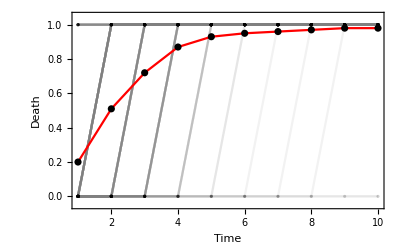

```mathematica
deathstoplot=Table[storebarchartdata⟦i,4⟧,{i,Range[batchruns]}];
Show[{ListPlot[deathstoplot,Joined->True,PlotStyle->Directive[Gray,Opacity[0.1]],PlotRange->{-0.01,1.01},Mesh->All,MeshStyle->{Black,Thickness[0.002]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Time", Black, 18],Style["Death",Black, 18]}],
ListPlot[deathstoplot//Mean,Joined->True,PlotStyle->Red,PlotRange->{-0.01,1.01},Mesh->All,MeshStyle->{Black,Thickness[0.002]},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Time", Black, 18],Style["Death",Black, 18]}]},PlotRange->{-0.05,1.05}]
```

```mathematica
ListPlot[Table[If[i==1||i==Length[counterlist],Callout[meandeath⟦i⟧,"t_pool = "<>ToString[counterlist⟦i⟧],If[i==1,{3,0.38},{1,0.8}]],meandeath⟦i⟧],{i,1,Length[meandeath]}],PlotLegends->counterlist⟦1;;⟧,PlotStyle->Table[{Darker[Hue[0.92,0.27,1.],i/Length[counterlist]],i/Length[counterlist]},{i,1,Length[counterlist]}](*{{Red,Full},{Red,Dashed},{Red,DotDashed}}*),PlotRange->{-0.05,1.05},Joined->True,MeshStyle->{Black,Thickness[0.002]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time", Black, 18],Style["Mean Death",Black, 18]}(*,GridLines->{None, {0.875}},GridLinesStyle->Directive[Red, Dashed,Thick]*)]
```

-Graphics-

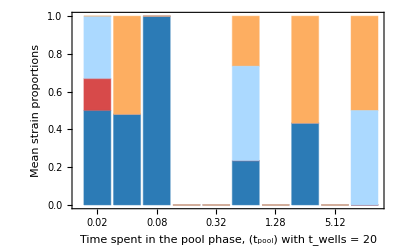

```mathematica
BarChart[Normalize[#,Total[#,∞]&]&/@Table[meanfrequenciesofstrains⟦i⟧//Last,{i,Length[meanfrequenciesofstrains]}],ChartLayout->"Stacked",ChartStyle->base,Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Time spent in the pool phase, (t_pool)\n with t_wells = "<>ToString[tmax], Black,18],Style["Mean strain proportions",Black,18]},
ChartLabels->{counterlist,None}(*,PlotLabel->Style["Equilibrium proportions",Black,24]*)]
```

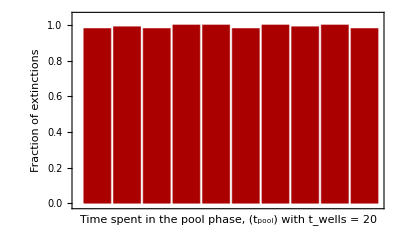

```mathematica
BarChart[Length[#]/batchruns&/@comparingextinctions,ChartStyle->Darker[Red],Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{Style["Time spent in the pool phase, (t_pool)\n with t_wells = "<>ToString[tmax], Black,18],Style["Fraction of extinctions",Black,18]},
ChartLabels->{counterlist,None}(*,PlotLabel->Style["Equilibrium proportions",Black,24]*),PlotRange->{All,{-0.01,1.05}}]
```

Run the above code multiple times by changing the startfeedback at for batchsize>1 and store the results in the following variables to generate the histogram and the piechart

```mathematica
feedbackat9=extinction;
```

```mathematica
feedbackat5=extinction;
```

```mathematica
feedbackat0=extinction;
```

```mathematica
Histogram[{feedbackat0,feedbackat5,feedbackat9},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Time of extinction", Black, 18],Style["Extinction events",Black, 18]},PlotRange->{{0.5,10.5},{0,100}},ChartStyle->{{HatchFilling[90 Degree,1,4],HatchFilling[-20 Degree,1,4],HatchFilling[20 Degree,1,4]},{Darker[Red],Darker[Red],Darker[Red]}}]
```

-Graphics-

```mathematica
PieChart[{{100-Length[feedbackat0],Length[feedbackat0]},{100-Length[feedbackat5],Length[feedbackat5]},{100-Length[feedbackat9],Length[feedbackat9]}},ChartLabels->{"",Style["Extinction",White, 8]},ChartStyle->{White,Darker[Red]},Background->White]
```

-Graphics-